### Задача 6

Произведено n выстрелов с постоянной вероятностью попадания при каждом выстреле, равной р.
Для случайной величины m (числа попаданий в цель) найти:
1) распределение вероятностей,
2) функцию распределения и построить её график,
3) вероятность попадания случайной величины в интервал ]α,β[,
4) найти математическое ожидание, дисперсию, среднее квадратическое отклонение случайной величины ξ.

Дано:

n=4, p=0.4,   ]α,β[ =  ]1.5, 2.5[

1)Так как мы имеем последовательность из n независимых случайных экспериментов, таких, что вероятность успеха в каждом из них постоянна, то мы имеем дела с биномиальным распределением.

2) Функция распределения имеет вид:

p_y(k)=C_n^k(p^k(1-p))^(n-k)

Построим её:

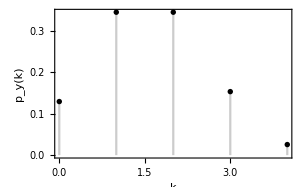

```mathematica
DiscretePlot[PDF[BinomialDistribution[4,0.4],t],{t,0,4},Frame->True,PlotTheme->"Monochrome",FrameLabel->{"k","p_y(k)"}]
```

3)